MAProcess[0.00393089,{0.492309,0.416546,0.286254},0.251656]

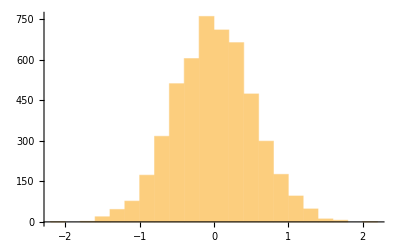

| Statistic | P-Value
Anderson-Darling | 0.283113 | 0.660557
Baringhaus-Henze | 0.540615 | 0.549279
Cramér-von Mises | 0.0370847 | 0.72982
Jarque-Bera ALM | 0.156922 | 0.924388
Kolmogorov-Smirnov | 0.00725528 | 0.787848
Kuiper | 0.0137296 | 0.678854
Mardia Combined | 0.156922 | 0.924388
Mardia Kurtosis | 0.137645 | 0.890521
Mardia Skewness | 0.132677 | 0.715672
Pearson χ^2 | 59.6803 | 0.414363
Shapiro-Wilk | 0.999721 | 0.769608
Watson U^2 | 0.0368443 | 0.682736

```mathematica
data = TemporalData[1];
model=EstimatedProcess[data,MAProcess[3]]
residuals=Rest[data["PathStates"]-KalmanFilter[model,data]["PathStates"]];
Histogram[residuals]
DistributionFitTest[residuals,Automatic,{"TestDataTable",All}]
```